```mathematica
Import["C:\\Users\\jhenry1\\Documents\\GitHub\\QM_prisoners_dilemma\\Mathematica\\StrategySpaces.wl"]
Import["C:\\Users\\jhenry1\\Documents\\GitHub\\QM_prisoners_dilemma\\Mathematica\\QPD_dynamics.wl"]
Import["C:\\Users\\jhenry1\\Documents\\GitHub\\QM_prisoners_dilemma\\Mathematica\\DiscreteNashEqulibrium.wl"]
```

```mathematica
binaryOctahedralGroup//Length
```

48

```mathematica
o = DeleteDuplicates[binaryOctahedralGroup,(#1==#2||#1==-#2)&];
```

```mathematica
Length[o]
```

24

## a=b=0 γ=π/2

```mathematica
strategyGroup = o;
symmetricJ = FullSimplify[(J[0,0,Pi/2]//FullSimplify),Assumptions->0<γ<π/2];
```

```mathematica
finalStates = FullSimplify[Table[play[symmetricJ,strategyGroup[[i]],strategyGroup[[j]]],{i,24},{j,24}]/.Conjugate->MyConj];
```

```mathematica
alicesScores = FullSimplify[(Map[alicesScore,finalStates,{2}]/.Conjugate->MyConj)//Simplify];
bobsScores = FullSimplify[(Map[bobsScore,finalStates,{2}]/.Conjugate->MyConj)//Simplify];
```

```mathematica
alicesScores//MatrixForm
bobsScores//MatrixForm
```

(3 | 2 | 9/4 | 1/2 | 9/4 | 3/2 | 1 | 2 | 9/4 | 4 | 9/4 | 3 | 0 | 5/2 | 9/4 | 4 | 9/4 | 3/2 | 5 | 5/2 | 9/4 | 1/2 | 9/4 | 3
2 | 1 | 1/2 | 9/4 | 3/2 | 9/4 | 2 | 3 | 4 | 9/4 | 3 | 9/4 | 5/2 | 5 | 4 | 9/4 | 3/2 | 9/4 | 5/2 | 0 | 1/2 | 9/4 | 3 | 9/4
9/4 | 3 | 9/4 | 2 | 3 | 4 | 9/4 | 3/2 | 9/4 | 2 | 1 | 1/2 | 9/4 | 3 | 9/4 | 5/2 | 0 | 1/2 | 9/4 | 3/2 | 9/4 | 5/2 | 5 | 4
3 | 9/4 | 2 | 9/4 | 4 | 5 | 3/2 | 9/4 | 2 | 9/4 | 1/2 | 0 | 3 | 9/4 | 5/2 | 9/4 | 1/2 | 1 | 3/2 | 9/4 | 5/2 | 9/4 | 4 | 3
9/4 | 4 | 3 | 3/2 | 9/4 | 5/2 | 9/4 | 1/2 | 1 | 3 | 9/4 | 5/2 | 9/4 | 1/2 | 0 | 3/2 | 9/4 | 2 | 9/4 | 4 | 5 | 3 | 9/4 | 2
4 | 9/4 | 3/2 | 0 | 5/2 | 9/4 | 1/2 | 9/4 | 3 | 5 | 5/2 | 9/4 | 1/2 | 9/4 | 3/2 | 3 | 2 | 9/4 | 4 | 9/4 | 3 | 1 | 2 | 9/4
1 | 2 | 9/4 | 4 | 9/4 | 3 | 3 | 2 | 9/4 | 1/2 | 9/4 | 3/2 | 5 | 5/2 | 9/4 | 1/2 | 9/4 | 3 | 0 | 5/2 | 9/4 | 4 | 9/4 | 3/2
2 | 3 | 4 | 9/4 | 3 | 9/4 | 2 | 1 | 1/2 | 9/4 | 3/2 | 9/4 | 5/2 | 0 | 1/2 | 9/4 | 3 | 9/4 | 5/2 | 5 | 4 | 9/4 | 3/2 | 9/4
9/4 | 3/2 | 9/4 | 2 | 1 | 1/2 | 9/4 | 3 | 9/4 | 2 | 3 | 4 | 9/4 | 3/2 | 9/4 | 5/2 | 5 | 4 | 9/4 | 3 | 9/4 | 5/2 | 0 | 1/2
3/2 | 9/4 | 2 | 9/4 | 1/2 | 0 | 3 | 9/4 | 2 | 9/4 | 4 | 5 | 3/2 | 9/4 | 5/2 | 9/4 | 4 | 3 | 3 | 9/4 | 5/2 | 9/4 | 1/2 | 1
9/4 | 1/2 | 1 | 3 | 9/4 | 5/2 | 9/4 | 4 | 3 | 3/2 | 9/4 | 5/2 | 9/4 | 4 | 5 | 3 | 9/4 | 2 | 9/4 | 1/2 | 0 | 3/2 | 9/4 | 2
1/2 | 9/4 | 3 | 5 | 5/2 | 9/4 | 4 | 9/4 | 3/2 | 0 | 5/2 | 9/4 | 4 | 9/4 | 3 | 1 | 2 | 9/4 | 1/2 | 9/4 | 3/2 | 3 | 2 | 9/4
5 | 5/2 | 9/4 | 1/2 | 9/4 | 3 | 0 | 5/2 | 9/4 | 4 | 9/4 | 3/2 | 1 | 2 | 9/4 | 4 | 9/4 | 3 | 3 | 2 | 9/4 | 1/2 | 9/4 | 3/2
5/2 | 0 | 1/2 | 9/4 | 3 | 9/4 | 5/2 | 5 | 4 | 9/4 | 3/2 | 9/4 | 2 | 3 | 4 | 9/4 | 3 | 9/4 | 2 | 1 | 1/2 | 9/4 | 3/2 | 9/4
9/4 | 3/2 | 9/4 | 5/2 | 5 | 4 | 9/4 | 3 | 9/4 | 5/2 | 0 | 1/2 | 9/4 | 3/2 | 9/4 | 2 | 1 | 1/2 | 9/4 | 3 | 9/4 | 2 | 3 | 4
3/2 | 9/4 | 5/2 | 9/4 | 4 | 3 | 3 | 9/4 | 5/2 | 9/4 | 1/2 | 1 | 3/2 | 9/4 | 2 | 9/4 | 1/2 | 0 | 3 | 9/4 | 2 | 9/4 | 4 | 5
9/4 | 4 | 5 | 3 | 9/4 | 2 | 9/4 | 1/2 | 0 | 3/2 | 9/4 | 2 | 9/4 | 1/2 | 1 | 3 | 9/4 | 5/2 | 9/4 | 4 | 3 | 3/2 | 9/4 | 5/2
4 | 9/4 | 3 | 1 | 2 | 9/4 | 1/2 | 9/4 | 3/2 | 3 | 2 | 9/4 | 1/2 | 9/4 | 3 | 5 | 5/2 | 9/4 | 4 | 9/4 | 3/2 | 0 | 5/2 | 9/4
0 | 5/2 | 9/4 | 4 | 9/4 | 3/2 | 5 | 5/2 | 9/4 | 1/2 | 9/4 | 3 | 3 | 2 | 9/4 | 1/2 | 9/4 | 3/2 | 1 | 2 | 9/4 | 4 | 9/4 | 3
5/2 | 5 | 4 | 9/4 | 3/2 | 9/4 | 5/2 | 0 | 1/2 | 9/4 | 3 | 9/4 | 2 | 1 | 1/2 | 9/4 | 3/2 | 9/4 | 2 | 3 | 4 | 9/4 | 3 | 9/4
9/4 | 3 | 9/4 | 5/2 | 0 | 1/2 | 9/4 | 3/2 | 9/4 | 5/2 | 5 | 4 | 9/4 | 3 | 9/4 | 2 | 3 | 4 | 9/4 | 3/2 | 9/4 | 2 | 1 | 1/2
3 | 9/4 | 5/2 | 9/4 | 1/2 | 1 | 3/2 | 9/4 | 5/2 | 9/4 | 4 | 3 | 3 | 9/4 | 2 | 9/4 | 4 | 5 | 3/2 | 9/4 | 2 | 9/4 | 1/2 | 0
9/4 | 1/2 | 0 | 3/2 | 9/4 | 2 | 9/4 | 4 | 5 | 3 | 9/4 | 2 | 9/4 | 4 | 3 | 3/2 | 9/4 | 5/2 | 9/4 | 1/2 | 1 | 3 | 9/4 | 5/2
1/2 | 9/4 | 3/2 | 3 | 2 | 9/4 | 4 | 9/4 | 3 | 1 | 2 | 9/4 | 4 | 9/4 | 3/2 | 0 | 5/2 | 9/4 | 1/2 | 9/4 | 3 | 5 | 5/2 | 9/4)

(3 | 2 | 9/4 | 3 | 9/4 | 4 | 1 | 2 | 9/4 | 3/2 | 9/4 | 1/2 | 5 | 5/2 | 9/4 | 3/2 | 9/4 | 4 | 0 | 5/2 | 9/4 | 3 | 9/4 | 1/2
2 | 1 | 3 | 9/4 | 4 | 9/4 | 2 | 3 | 3/2 | 9/4 | 1/2 | 9/4 | 5/2 | 0 | 3/2 | 9/4 | 4 | 9/4 | 5/2 | 5 | 3 | 9/4 | 1/2 | 9/4
9/4 | 1/2 | 9/4 | 2 | 3 | 3/2 | 9/4 | 4 | 9/4 | 2 | 1 | 3 | 9/4 | 1/2 | 9/4 | 5/2 | 5 | 3 | 9/4 | 4 | 9/4 | 5/2 | 0 | 3/2
1/2 | 9/4 | 2 | 9/4 | 3/2 | 0 | 4 | 9/4 | 2 | 9/4 | 3 | 5 | 1/2 | 9/4 | 5/2 | 9/4 | 3 | 1 | 4 | 9/4 | 5/2 | 9/4 | 3/2 | 3
9/4 | 3/2 | 3 | 4 | 9/4 | 5/2 | 9/4 | 3 | 1 | 1/2 | 9/4 | 5/2 | 9/4 | 3 | 5 | 4 | 9/4 | 2 | 9/4 | 3/2 | 0 | 1/2 | 9/4 | 2
3/2 | 9/4 | 4 | 5 | 5/2 | 9/4 | 3 | 9/4 | 1/2 | 0 | 5/2 | 9/4 | 3 | 9/4 | 4 | 3 | 2 | 9/4 | 3/2 | 9/4 | 1/2 | 1 | 2 | 9/4
1 | 2 | 9/4 | 3/2 | 9/4 | 1/2 | 3 | 2 | 9/4 | 3 | 9/4 | 4 | 0 | 5/2 | 9/4 | 3 | 9/4 | 1/2 | 5 | 5/2 | 9/4 | 3/2 | 9/4 | 4
2 | 3 | 3/2 | 9/4 | 1/2 | 9/4 | 2 | 1 | 3 | 9/4 | 4 | 9/4 | 5/2 | 5 | 3 | 9/4 | 1/2 | 9/4 | 5/2 | 0 | 3/2 | 9/4 | 4 | 9/4
9/4 | 4 | 9/4 | 2 | 1 | 3 | 9/4 | 1/2 | 9/4 | 2 | 3 | 3/2 | 9/4 | 4 | 9/4 | 5/2 | 0 | 3/2 | 9/4 | 1/2 | 9/4 | 5/2 | 5 | 3
4 | 9/4 | 2 | 9/4 | 3 | 5 | 1/2 | 9/4 | 2 | 9/4 | 3/2 | 0 | 4 | 9/4 | 5/2 | 9/4 | 3/2 | 3 | 1/2 | 9/4 | 5/2 | 9/4 | 3 | 1
9/4 | 3 | 1 | 1/2 | 9/4 | 5/2 | 9/4 | 3/2 | 3 | 4 | 9/4 | 5/2 | 9/4 | 3/2 | 0 | 1/2 | 9/4 | 2 | 9/4 | 3 | 5 | 4 | 9/4 | 2
3 | 9/4 | 1/2 | 0 | 5/2 | 9/4 | 3/2 | 9/4 | 4 | 5 | 5/2 | 9/4 | 3/2 | 9/4 | 1/2 | 1 | 2 | 9/4 | 3 | 9/4 | 4 | 3 | 2 | 9/4
0 | 5/2 | 9/4 | 3 | 9/4 | 1/2 | 5 | 5/2 | 9/4 | 3/2 | 9/4 | 4 | 1 | 2 | 9/4 | 3/2 | 9/4 | 1/2 | 3 | 2 | 9/4 | 3 | 9/4 | 4
5/2 | 5 | 3 | 9/4 | 1/2 | 9/4 | 5/2 | 0 | 3/2 | 9/4 | 4 | 9/4 | 2 | 3 | 3/2 | 9/4 | 1/2 | 9/4 | 2 | 1 | 3 | 9/4 | 4 | 9/4
9/4 | 4 | 9/4 | 5/2 | 0 | 3/2 | 9/4 | 1/2 | 9/4 | 5/2 | 5 | 3 | 9/4 | 4 | 9/4 | 2 | 1 | 3 | 9/4 | 1/2 | 9/4 | 2 | 3 | 3/2
4 | 9/4 | 5/2 | 9/4 | 3/2 | 3 | 1/2 | 9/4 | 5/2 | 9/4 | 3 | 1 | 4 | 9/4 | 2 | 9/4 | 3 | 5 | 1/2 | 9/4 | 2 | 9/4 | 3/2 | 0
9/4 | 3/2 | 0 | 1/2 | 9/4 | 2 | 9/4 | 3 | 5 | 4 | 9/4 | 2 | 9/4 | 3 | 1 | 1/2 | 9/4 | 5/2 | 9/4 | 3/2 | 3 | 4 | 9/4 | 5/2
3/2 | 9/4 | 1/2 | 1 | 2 | 9/4 | 3 | 9/4 | 4 | 3 | 2 | 9/4 | 3 | 9/4 | 1/2 | 0 | 5/2 | 9/4 | 3/2 | 9/4 | 4 | 5 | 5/2 | 9/4
5 | 5/2 | 9/4 | 3/2 | 9/4 | 4 | 0 | 5/2 | 9/4 | 3 | 9/4 | 1/2 | 3 | 2 | 9/4 | 3 | 9/4 | 4 | 1 | 2 | 9/4 | 3/2 | 9/4 | 1/2
5/2 | 0 | 3/2 | 9/4 | 4 | 9/4 | 5/2 | 5 | 3 | 9/4 | 1/2 | 9/4 | 2 | 1 | 3 | 9/4 | 4 | 9/4 | 2 | 3 | 3/2 | 9/4 | 1/2 | 9/4
9/4 | 1/2 | 9/4 | 5/2 | 5 | 3 | 9/4 | 4 | 9/4 | 5/2 | 0 | 3/2 | 9/4 | 1/2 | 9/4 | 2 | 3 | 3/2 | 9/4 | 4 | 9/4 | 2 | 1 | 3
1/2 | 9/4 | 5/2 | 9/4 | 3 | 1 | 4 | 9/4 | 5/2 | 9/4 | 3/2 | 3 | 1/2 | 9/4 | 2 | 9/4 | 3/2 | 0 | 4 | 9/4 | 2 | 9/4 | 3 | 5
9/4 | 3 | 5 | 4 | 9/4 | 2 | 9/4 | 3/2 | 0 | 1/2 | 9/4 | 2 | 9/4 | 3/2 | 3 | 4 | 9/4 | 5/2 | 9/4 | 3 | 1 | 1/2 | 9/4 | 5/2
3 | 9/4 | 4 | 3 | 2 | 9/4 | 3/2 | 9/4 | 1/2 | 1 | 2 | 9/4 | 3/2 | 9/4 | 4 | 5 | 5/2 | 9/4 | 3 | 9/4 | 1/2 | 0 | 5/2 | 9/4)

```mathematica
eq = DiscreteNashEquilibria[(alicesScores),(bobsScores),0<γ<Pi/2];
```

```mathematica
simplifiedEQ= (FullSimplify[{#[[1]],#[[2]],Reduce[#[[3]]]},Assumptions->0<γ<π/2]&/@eq);
```

```mathematica
simplifiedEQ
```

{}

## a=b=0

```mathematica
strategyGroup = o
```

{{{1,0},{0,1}},{{(1+ⅈ)/(√2),0},{0,(1-ⅈ)/(√2)}},{{1/2+ⅈ/2,1/2+ⅈ/2},{-1/2+ⅈ/2,1/2-ⅈ/2}},{{ⅈ/(√2),1/(√2)},{-1/(√2),-ⅈ/(√2)}},{{-1/2+ⅈ/2,1/2+ⅈ/2},{-1/2+ⅈ/2,-1/2-ⅈ/2}},{{-1/(√2),1/(√2)},{-1/(√2),-1/(√2)}},{{ⅈ,0},{0,-ⅈ}},{{-(1-ⅈ)/(√2),0},{0,-(1+ⅈ)/(√2)}},{{-1/2+ⅈ/2,-1/2+ⅈ/2},{1/2+ⅈ/2,-1/2-ⅈ/2}},{{-1/(√2),ⅈ/(√2)},{ⅈ/(√2),-1/(√2)}},{{-1/2-ⅈ/2,-1/2+ⅈ/2},{1/2+ⅈ/2,-1/2+ⅈ/2}},{{-ⅈ/(√2),ⅈ/(√2)},{ⅈ/(√2),ⅈ/(√2)}},{{0,1},{-1,0}},{{0,(1-ⅈ)/(√2)},{-(1+ⅈ)/(√2),0}},{{-1/2+ⅈ/2,1/2-ⅈ/2},{-1/2-ⅈ/2,-1/2-ⅈ/2}},{{-1/(√2),-ⅈ/(√2)},{-ⅈ/(√2),-1/(√2)}},{{-1/2+ⅈ/2,-1/2-ⅈ/2},{1/2-ⅈ/2,-1/2-ⅈ/2}},{{-1/(√2),-1/(√2)},{1/(√2),-1/(√2)}},{{0,ⅈ},{ⅈ,0}},{{0,(1+ⅈ)/(√2)},{-(1-ⅈ)/(√2),0}},{{-1/2-ⅈ/2,1/2+ⅈ/2},{-1/2+ⅈ/2,-1/2+ⅈ/2}},{{-ⅈ/(√2),1/(√2)},{-1/(√2),ⅈ/(√2)}},{{-1/2-ⅈ/2,1/2-ⅈ/2},{-1/2-ⅈ/2,-1/2+ⅈ/2}},{{-ⅈ/(√2),-ⅈ/(√2)},{-ⅈ/(√2),ⅈ/(√2)}}}

```mathematica
symmetricJ = FullSimplify[(J[0,0,γ]//FullSimplify),Assumptions->0<γ<π/2];
```

```mathematica
finalStates = FullSimplify[Table[play[symmetricJ,strategyGroup[[i]],strategyGroup[[j]]],{i,24},{j,24}]/.Conjugate->MyConj];
```

```mathematica
alicesScores = FullSimplify[(Map[alicesScore,finalStates,{2}]/.Conjugate->MyConj)//Simplify];
bobsScores = FullSimplify[(Map[bobsScore,finalStates,{2}]/.Conjugate->MyConj)//Simplify];
```

```mathematica
alicesScores//MatrixForm
```

(3 | 1/2 (5+Cos[2 γ]) | -3/8 (-5+Cos[2 γ]) | 1/2 (2+Cos[2 γ]) | -3/8 (-5+Cos[2 γ]) | 3/2 | 2+Cos[2 γ] | 1/2 (5+Cos[2 γ]) | -3/8 (-5+Cos[2 γ]) | 1/2 (3+5 Sin[γ]^2) | -3/8 (-5+Cos[2 γ]) | -3/4 (-3+Cos[2 γ]) | 0 | (5 Sin[γ]^2)/2 | -3/8 (-5+Cos[2 γ]) | 1/2 (3+5 Sin[γ]^2) | -3/8 (-5+Cos[2 γ]) | 3/2 | 5 Sin[γ]^2 | (5 Sin[γ]^2)/2 | -3/8 (-5+Cos[2 γ]) | 1/2 (2+Cos[2 γ]) | -3/8 (-5+Cos[2 γ]) | -3/4 (-3+Cos[2 γ])
1/2 (5+Cos[2 γ]) | 2+Cos[2 γ] | 1/2 (2+Cos[2 γ]) | -3/8 (-5+Cos[2 γ]) | 3/2 | -3/8 (-5+Cos[2 γ]) | 1/2 (5+Cos[2 γ]) | 3 | 1/2 (3+5 Sin[γ]^2) | -3/8 (-5+Cos[2 γ]) | -3/4 (-3+Cos[2 γ]) | -3/8 (-5+Cos[2 γ]) | (5 Sin[γ]^2)/2 | 5 Sin[γ]^2 | 1/2 (3+5 Sin[γ]^2) | -3/8 (-5+Cos[2 γ]) | 3/2 | -3/8 (-5+Cos[2 γ]) | (5 Sin[γ]^2)/2 | 0 | 1/2 (2+Cos[2 γ]) | -3/8 (-5+Cos[2 γ]) | -3/4 (-3+Cos[2 γ]) | -3/8 (-5+Cos[2 γ])
1/8 (25+7 Cos[2 γ]) | 1/2 (7+Cos[2 γ]) | 9/4 | 1/4 (9-Sin[γ]) | 3/8 (5+Cos[2 γ]+4 Sin[γ]) | 1/4 (9+7 Sin[γ]) | 1/8 (25+7 Cos[2 γ]) | 1/2 (3+5 Cos[γ]^2) | 9/4 | 1/4 (9-Sin[γ]) | -3/8 (-7+Cos[2 γ])-2 Sin[γ] | 1/4 (9-7 Sin[γ]) | 1/8 (11-7 Cos[2 γ]) | 1/2 (1+5 Sin[γ]^2) | 9/4 | 1/4 (9+Sin[γ]) | 3/8 (5+Cos[2 γ]-4 Sin[γ]) | 1/4 (9-7 Sin[γ]) | 1/8 (11-7 Cos[2 γ]) | 1-1/2 Cos[2 γ] | 9/4 | 1/4 (9+Sin[γ]) | -3/8 (-7+Cos[2 γ])+2 Sin[γ] | 1/4 (9+7 Sin[γ])
1/2 (7+Cos[2 γ]) | 1/8 (25+7 Cos[2 γ]) | 1/4 (9-Sin[γ]) | 9/4 | 1/4 (9+7 Sin[γ]) | -3/8 (-7+Cos[2 γ])+2 Sin[γ] | 1/2 (3+5 Cos[γ]^2) | 1/8 (25+7 Cos[2 γ]) | 1/4 (9-Sin[γ]) | 9/4 | 1/4 (9-7 Sin[γ]) | 3/8 (5+Cos[2 γ]-4 Sin[γ]) | 1/2 (1+5 Sin[γ]^2) | 1/8 (11-7 Cos[2 γ]) | 1/4 (9+Sin[γ]) | 9/4 | 1/4 (9-7 Sin[γ]) | -3/8 (-7+Cos[2 γ])-2 Sin[γ] | 1-1/2 Cos[2 γ] | 1/8 (11-7 Cos[2 γ]) | 1/4 (9+Sin[γ]) | 9/4 | 1/4 (9+7 Sin[γ]) | 3/8 (5+Cos[2 γ]+4 Sin[γ])
1/8 (25+7 Cos[2 γ]) | 4 | 1/8 (25-7 Cos[2 γ]-8 Sin[γ]) | -3/4 (-3+Sin[γ]) | 9/4 | 1/4 (9+Sin[γ]) | 1/8 (25+7 Cos[2 γ]) | 1/4 (9+7 Cos[2 γ]) | 1/4 (8 Cos[γ]^2+(1+Sin[γ])^2) | 3/4 (3+Sin[γ]) | 9/4 | 1/4 (9+Sin[γ]) | 1/8 (11-7 Cos[2 γ]) | 1/2 | 2 Cos[γ]^2+1/4 (-1+Sin[γ])^2 | -3/4 (-3+Sin[γ]) | 9/4 | 1/4 (9-Sin[γ]) | 1/8 (11-7 Cos[2 γ]) | 1/4 (9-7 Cos[2 γ]) | 25/8-7/8 Cos[2 γ]+Sin[γ] | 3/4 (3+Sin[γ]) | 9/4 | 1/4 (9-Sin[γ])
4 | 1/8 (25+7 Cos[2 γ]) | -3/4 (-3+Sin[γ]) | 2 Cos[γ]^2+1/4 (-1+Sin[γ])^2 | 1/4 (9+Sin[γ]) | 9/4 | 1/4 (9+7 Cos[2 γ]) | 1/8 (25+7 Cos[2 γ]) | 3/4 (3+Sin[γ]) | 25/8-7/8 Cos[2 γ]+Sin[γ] | 1/4 (9+Sin[γ]) | 9/4 | 1/2 | 1/8 (11-7 Cos[2 γ]) | -3/4 (-3+Sin[γ]) | 1/8 (25-7 Cos[2 γ]-8 Sin[γ]) | 1/4 (9-Sin[γ]) | 9/4 | 1/4 (9-7 Cos[2 γ]) | 1/8 (11-7 Cos[2 γ]) | 3/4 (3+Sin[γ]) | 2 Cos[γ]^2+1/4 (1+Sin[γ])^2 | 1/4 (9-Sin[γ]) | 9/4
2+Cos[2 γ] | 1/2 (5+Cos[2 γ]) | -3/8 (-5+Cos[2 γ]) | 1/2 (3+5 Sin[γ]^2) | -3/8 (-5+Cos[2 γ]) | -3/4 (-3+Cos[2 γ]) | 3 | 1/2 (5+Cos[2 γ]) | -3/8 (-5+Cos[2 γ]) | 1/2 (2+Cos[2 γ]) | -3/8 (-5+Cos[2 γ]) | 3/2 | 5 Sin[γ]^2 | (5 Sin[γ]^2)/2 | -3/8 (-5+Cos[2 γ]) | 1/2 (2+Cos[2 γ]) | -3/8 (-5+Cos[2 γ]) | -3/4 (-3+Cos[2 γ]) | 0 | (5 Sin[γ]^2)/2 | -3/8 (-5+Cos[2 γ]) | 1/2 (3+5 Sin[γ]^2) | -3/8 (-5+Cos[2 γ]) | 3/2
1/2 (5+Cos[2 γ]) | 3 | 1/2 (3+5 Sin[γ]^2) | -3/8 (-5+Cos[2 γ]) | -3/4 (-3+Cos[2 γ]) | -3/8 (-5+Cos[2 γ]) | 1/2 (5+Cos[2 γ]) | 2+Cos[2 γ] | 1/2 (2+Cos[2 γ]) | -3/8 (-5+Cos[2 γ]) | 3/2 | -3/8 (-5+Cos[2 γ]) | (5 Sin[γ]^2)/2 | 0 | 1/2 (2+Cos[2 γ]) | -3/8 (-5+Cos[2 γ]) | -3/4 (-3+Cos[2 γ]) | -3/8 (-5+Cos[2 γ]) | (5 Sin[γ]^2)/2 | 5 Sin[γ]^2 | 1/2 (3+5 Sin[γ]^2) | -3/8 (-5+Cos[2 γ]) | 3/2 | -3/8 (-5+Cos[2 γ])
1/8 (25+7 Cos[2 γ]) | 1/2 (3+5 Cos[γ]^2) | 9/4 | 1/4 (9-Sin[γ]) | -3/8 (-7+Cos[2 γ])-2 Sin[γ] | 1/4 (9-7 Sin[γ]) | 1/8 (25+7 Cos[2 γ]) | 1/2 (7+Cos[2 γ]) | 9/4 | 1/4 (9-Sin[γ]) | 3/8 (5+Cos[2 γ]+4 Sin[γ]) | 1/4 (9+7 Sin[γ]) | 1/8 (11-7 Cos[2 γ]) | 1-1/2 Cos[2 γ] | 9/4 | 1/4 (9+Sin[γ]) | -3/8 (-7+Cos[2 γ])+2 Sin[γ] | 1/4 (9+7 Sin[γ]) | 1/8 (11-7 Cos[2 γ]) | 1/2 (1+5 Sin[γ]^2) | 9/4 | 1/4 (9+Sin[γ]) | 3/8 (5+Cos[2 γ]-4 Sin[γ]) | 1/4 (9-7 Sin[γ])
1/2 (3+5 Cos[γ]^2) | 1/8 (25+7 Cos[2 γ]) | 1/4 (9-Sin[γ]) | 9/4 | 1/4 (9-7 Sin[γ]) | 3/8 (5+Cos[2 γ]-4 Sin[γ]) | 1/2 (7+Cos[2 γ]) | 1/8 (25+7 Cos[2 γ]) | 1/4 (9-Sin[γ]) | 9/4 | 1/4 (9+7 Sin[γ]) | -3/8 (-7+Cos[2 γ])+2 Sin[γ] | 1-1/2 Cos[2 γ] | 1/8 (11-7 Cos[2 γ]) | 1/4 (9+Sin[γ]) | 9/4 | 1/4 (9+7 Sin[γ]) | 3/8 (5+Cos[2 γ]+4 Sin[γ]) | 1/2 (1+5 Sin[γ]^2) | 1/8 (11-7 Cos[2 γ]) | 1/4 (9+Sin[γ]) | 9/4 | 1/4 (9-7 Sin[γ]) | -3/8 (-7+Cos[2 γ])-2 Sin[γ]
1/8 (25+7 Cos[2 γ]) | 1/4 (9+7 Cos[2 γ]) | 1/4 (8 Cos[γ]^2+(1+Sin[γ])^2) | 3/4 (3+Sin[γ]) | 9/4 | 1/4 (9+Sin[γ]) | 1/8 (25+7 Cos[2 γ]) | 4 | 1/8 (25-7 Cos[2 γ]-8 Sin[γ]) | -3/4 (-3+Sin[γ]) | 9/4 | 1/4 (9+Sin[γ]) | 1/8 (11-7 Cos[2 γ]) | 1/4 (9-7 Cos[2 γ]) | 25/8-7/8 Cos[2 γ]+Sin[γ] | 3/4 (3+Sin[γ]) | 9/4 | 1/4 (9-Sin[γ]) | 1/8 (11-7 Cos[2 γ]) | 1/2 | 2 Cos[γ]^2+1/4 (-1+Sin[γ])^2 | -3/4 (-3+Sin[γ]) | 9/4 | 1/4 (9-Sin[γ])
1/4 (9+7 Cos[2 γ]) | 1/8 (25+7 Cos[2 γ]) | 3/4 (3+Sin[γ]) | 25/8-7/8 Cos[2 γ]+Sin[γ] | 1/4 (9+Sin[γ]) | 9/4 | 4 | 1/8 (25+7 Cos[2 γ]) | -3/4 (-3+Sin[γ]) | 2 Cos[γ]^2+1/4 (-1+Sin[γ])^2 | 1/4 (9+Sin[γ]) | 9/4 | 1/4 (9-7 Cos[2 γ]) | 1/8 (11-7 Cos[2 γ]) | 3/4 (3+Sin[γ]) | 2 Cos[γ]^2+1/4 (1+Sin[γ])^2 | 1/4 (9-Sin[γ]) | 9/4 | 1/2 | 1/8 (11-7 Cos[2 γ]) | -3/4 (-3+Sin[γ]) | 1/8 (25-7 Cos[2 γ]-8 Sin[γ]) | 1/4 (9-Sin[γ]) | 9/4
5 | 5/4 (3+Cos[2 γ]) | 3/8 (7+Cos[2 γ]) | 1/4 (7+5 Cos[2 γ]) | 3/8 (7+Cos[2 γ]) | 3 | 5 Cos[γ]^2 | 5/4 (3+Cos[2 γ]) | 3/8 (7+Cos[2 γ]) | 1/2 (7-Cos[2 γ]) | 3/8 (7+Cos[2 γ]) | 3/4 (3+Cos[2 γ]) | 1 | 1/2 (3-Cos[2 γ]) | 3/8 (7+Cos[2 γ]) | 1/2 (7-Cos[2 γ]) | 3/8 (7+Cos[2 γ]) | 3 | 2-Cos[2 γ] | 1/2 (3-Cos[2 γ]) | 3/8 (7+Cos[2 γ]) | 1/4 (7+5 Cos[2 γ]) | 3/8 (7+Cos[2 γ]) | 3/4 (3+Cos[2 γ])
5/4 (3+Cos[2 γ]) | 5 Cos[γ]^2 | 1/4 (7+5 Cos[2 γ]) | 3/8 (7+Cos[2 γ]) | 3 | 3/8 (7+Cos[2 γ]) | 5/4 (3+Cos[2 γ]) | 5 | 1/2 (7-Cos[2 γ]) | 3/8 (7+Cos[2 γ]) | 3/4 (3+Cos[2 γ]) | 3/8 (7+Cos[2 γ]) | 1/2 (3-Cos[2 γ]) | 2-Cos[2 γ] | 1/2 (7-Cos[2 γ]) | 3/8 (7+Cos[2 γ]) | 3 | 3/8 (7+Cos[2 γ]) | 1/2 (3-Cos[2 γ]) | 1 | 1/4 (7+5 Cos[2 γ]) | 3/8 (7+Cos[2 γ]) | 3/4 (3+Cos[2 γ]) | 3/8 (7+Cos[2 γ])
1/8 (25+7 Cos[2 γ]) | 1/2 (3+5 Cos[γ]^2) | 9/4 | 1/4 (9+Sin[γ]) | -3/8 (-7+Cos[2 γ])+2 Sin[γ] | 1/4 (9+7 Sin[γ]) | 1/8 (25+7 Cos[2 γ]) | 1/2 (7+Cos[2 γ]) | 9/4 | 1/4 (9+Sin[γ]) | 3/8 (5+Cos[2 γ]-4 Sin[γ]) | 1/4 (9-7 Sin[γ]) | 1/8 (11-7 Cos[2 γ]) | 1-1/2 Cos[2 γ] | 9/4 | 1/4 (9-Sin[γ]) | -3/8 (-7+Cos[2 γ])-2 Sin[γ] | 1/4 (9-7 Sin[γ]) | 1/8 (11-7 Cos[2 γ]) | 1/2 (1+5 Sin[γ]^2) | 9/4 | 1/4 (9-Sin[γ]) | 3/8 (5+Cos[2 γ]+4 Sin[γ]) | 1/4 (9+7 Sin[γ])
1/2 (3+5 Cos[γ]^2) | 1/8 (25+7 Cos[2 γ]) | 1/4 (9+Sin[γ]) | 9/4 | 1/4 (9+7 Sin[γ]) | 3/8 (5+Cos[2 γ]+4 Sin[γ]) | 1/2 (7+Cos[2 γ]) | 1/8 (25+7 Cos[2 γ]) | 1/4 (9+Sin[γ]) | 9/4 | 1/4 (9-7 Sin[γ]) | -3/8 (-7+Cos[2 γ])-2 Sin[γ] | 1-1/2 Cos[2 γ] | 1/8 (11-7 Cos[2 γ]) | 1/4 (9-Sin[γ]) | 9/4 | 1/4 (9-7 Sin[γ]) | 3/8 (5+Cos[2 γ]-4 Sin[γ]) | 1/2 (1+5 Sin[γ]^2) | 1/8 (11-7 Cos[2 γ]) | 1/4 (9-Sin[γ]) | 9/4 | 1/4 (9+7 Sin[γ]) | -3/8 (-7+Cos[2 γ])+2 Sin[γ]
1/8 (25+7 Cos[2 γ]) | 4 | 25/8-7/8 Cos[2 γ]+Sin[γ] | 3/4 (3+Sin[γ]) | 9/4 | 1/4 (9-Sin[γ]) | 1/8 (25+7 Cos[2 γ]) | 1/4 (9+7 Cos[2 γ]) | 2 Cos[γ]^2+1/4 (-1+Sin[γ])^2 | -3/4 (-3+Sin[γ]) | 9/4 | 1/4 (9-Sin[γ]) | 1/8 (11-7 Cos[2 γ]) | 1/2 | 1/4 (8 Cos[γ]^2+(1+Sin[γ])^2) | 3/4 (3+Sin[γ]) | 9/4 | 1/4 (9+Sin[γ]) | 1/8 (11-7 Cos[2 γ]) | 1/4 (9-7 Cos[2 γ]) | 1/8 (25-7 Cos[2 γ]-8 Sin[γ]) | -3/4 (-3+Sin[γ]) | 9/4 | 1/4 (9+Sin[γ])
4 | 1/8 (25+7 Cos[2 γ]) | 3/4 (3+Sin[γ]) | 1/4 (8 Cos[γ]^2+(1+Sin[γ])^2) | 1/4 (9-Sin[γ]) | 9/4 | 1/4 (9+7 Cos[2 γ]) | 1/8 (25+7 Cos[2 γ]) | -3/4 (-3+Sin[γ]) | 1/8 (25-7 Cos[2 γ]-8 Sin[γ]) | 1/4 (9-Sin[γ]) | 9/4 | 1/2 | 1/8 (11-7 Cos[2 γ]) | 3/4 (3+Sin[γ]) | 25/8-7/8 Cos[2 γ]+Sin[γ] | 1/4 (9+Sin[γ]) | 9/4 | 1/4 (9-7 Cos[2 γ]) | 1/8 (11-7 Cos[2 γ]) | -3/4 (-3+Sin[γ]) | 2 Cos[γ]^2+1/4 (-1+Sin[γ])^2 | 1/4 (9+Sin[γ]) | 9/4
5 Cos[γ]^2 | 5/4 (3+Cos[2 γ]) | 3/8 (7+Cos[2 γ]) | 1/2 (7-Cos[2 γ]) | 3/8 (7+Cos[2 γ]) | 3/4 (3+Cos[2 γ]) | 5 | 5/4 (3+Cos[2 γ]) | 3/8 (7+Cos[2 γ]) | 1/4 (7+5 Cos[2 γ]) | 3/8 (7+Cos[2 γ]) | 3 | 2-Cos[2 γ] | 1/2 (3-Cos[2 γ]) | 3/8 (7+Cos[2 γ]) | 1/4 (7+5 Cos[2 γ]) | 3/8 (7+Cos[2 γ]) | 3/4 (3+Cos[2 γ]) | 1 | 1/2 (3-Cos[2 γ]) | 3/8 (7+Cos[2 γ]) | 1/2 (7-Cos[2 γ]) | 3/8 (7+Cos[2 γ]) | 3
5/4 (3+Cos[2 γ]) | 5 | 1/2 (7-Cos[2 γ]) | 3/8 (7+Cos[2 γ]) | 3/4 (3+Cos[2 γ]) | 3/8 (7+Cos[2 γ]) | 5/4 (3+Cos[2 γ]) | 5 Cos[γ]^2 | 1/4 (7+5 Cos[2 γ]) | 3/8 (7+Cos[2 γ]) | 3 | 3/8 (7+Cos[2 γ]) | 1/2 (3-Cos[2 γ]) | 1 | 1/4 (7+5 Cos[2 γ]) | 3/8 (7+Cos[2 γ]) | 3/4 (3+Cos[2 γ]) | 3/8 (7+Cos[2 γ]) | 1/2 (3-Cos[2 γ]) | 2-Cos[2 γ] | 1/2 (7-Cos[2 γ]) | 3/8 (7+Cos[2 γ]) | 3 | 3/8 (7+Cos[2 γ])
1/8 (25+7 Cos[2 γ]) | 1/2 (7+Cos[2 γ]) | 9/4 | 1/4 (9+Sin[γ]) | 3/8 (5+Cos[2 γ]-4 Sin[γ]) | 1/4 (9-7 Sin[γ]) | 1/8 (25+7 Cos[2 γ]) | 1/2 (3+5 Cos[γ]^2) | 9/4 | 1/4 (9+Sin[γ]) | -3/8 (-7+Cos[2 γ])+2 Sin[γ] | 1/4 (9+7 Sin[γ]) | 1/8 (11-7 Cos[2 γ]) | 1/2 (1+5 Sin[γ]^2) | 9/4 | 1/4 (9-Sin[γ]) | 3/8 (5+Cos[2 γ]+4 Sin[γ]) | 1/4 (9+7 Sin[γ]) | 1/8 (11-7 Cos[2 γ]) | 1-1/2 Cos[2 γ] | 9/4 | 1/4 (9-Sin[γ]) | -3/8 (-7+Cos[2 γ])-2 Sin[γ] | 1/4 (9-7 Sin[γ])
1/2 (7+Cos[2 γ]) | 1/8 (25+7 Cos[2 γ]) | 1/4 (9+Sin[γ]) | 9/4 | 1/4 (9-7 Sin[γ]) | -3/8 (-7+Cos[2 γ])-2 Sin[γ] | 1/2 (3+5 Cos[γ]^2) | 1/8 (25+7 Cos[2 γ]) | 1/4 (9+Sin[γ]) | 9/4 | 1/4 (9+7 Sin[γ]) | 3/8 (5+Cos[2 γ]+4 Sin[γ]) | 1/2 (1+5 Sin[γ]^2) | 1/8 (11-7 Cos[2 γ]) | 1/4 (9-Sin[γ]) | 9/4 | 1/4 (9+7 Sin[γ]) | -3/8 (-7+Cos[2 γ])+2 Sin[γ] | 1-1/2 Cos[2 γ] | 1/8 (11-7 Cos[2 γ]) | 1/4 (9-Sin[γ]) | 9/4 | 1/4 (9-7 Sin[γ]) | 3/8 (5+Cos[2 γ]-4 Sin[γ])
1/8 (25+7 Cos[2 γ]) | 1/4 (9+7 Cos[2 γ]) | 2 Cos[γ]^2+1/4 (-1+Sin[γ])^2 | -3/4 (-3+Sin[γ]) | 9/4 | 1/4 (9-Sin[γ]) | 1/8 (25+7 Cos[2 γ]) | 4 | 25/8-7/8 Cos[2 γ]+Sin[γ] | 3/4 (3+Sin[γ]) | 9/4 | 1/4 (9-Sin[γ]) | 1/8 (11-7 Cos[2 γ]) | 1/4 (9-7 Cos[2 γ]) | 1/8 (25-7 Cos[2 γ]-8 Sin[γ]) | -3/4 (-3+Sin[γ]) | 9/4 | 1/4 (9+Sin[γ]) | 1/8 (11-7 Cos[2 γ]) | 1/2 | 2 Cos[γ]^2+1/4 (1+Sin[γ])^2 | 3/4 (3+Sin[γ]) | 9/4 | 1/4 (9+Sin[γ])
1/4 (9+7 Cos[2 γ]) | 1/8 (25+7 Cos[2 γ]) | -3/4 (-3+Sin[γ]) | 1/8 (25-7 Cos[2 γ]-8 Sin[γ]) | 1/4 (9-Sin[γ]) | 9/4 | 4 | 1/8 (25+7 Cos[2 γ]) | 3/4 (3+Sin[γ]) | 2 Cos[γ]^2+1/4 (1+Sin[γ])^2 | 1/4 (9-Sin[γ]) | 9/4 | 1/4 (9-7 Cos[2 γ]) | 1/8 (11-7 Cos[2 γ]) | -3/4 (-3+Sin[γ]) | 2 Cos[γ]^2+1/4 (-1+Sin[γ])^2 | 1/4 (9+Sin[γ]) | 9/4 | 1/2 | 1/8 (11-7 Cos[2 γ]) | 3/4 (3+Sin[γ]) | 25/8-7/8 Cos[2 γ]+Sin[γ] | 1/4 (9+Sin[γ]) | 9/4)

```mathematica
(* ---- Usage ---- *)

(* Original version, now with the variables passed explicitly *)
eq = DiscreteNashEquilibria[alicesScores, bobsScores,
   0 < γ < Pi/2, {a, γ}];

(* Algebraic version: replace Sin[γ], Cos[γ] with s, c *)
toAlg = Expand[TrigExpand[#] /. {Sin[γ] -> s, Cos[γ] -> c}] &;
algA = toAlg[alicesScores];
algB = toAlg[bobsScores];
FreeQ[{algA, algB}, γ]   (* must be True before going on *)

eqAlg = DiscreteNashEquilibria[algA, algB,
   c^2 + s^2 == 1 && c > 0 && s > 0, {a, c, s}];
```

True

```mathematica
eqAlg/.{c->Cos[γ],s->Sin[γ]}//FullSimplify
```

{{{13,19},{2-Cos[2 γ],2-Cos[2 γ]},√(2/3)≤Cos[γ]<1&&√(Sin[γ]^2)==Sin[γ]},{{14,14},{2-Cos[2 γ],2-Cos[2 γ]},√(2/3)≤Cos[γ]<1&&√(Sin[γ]^2)==Sin[γ]},{{19,13},{2-Cos[2 γ],2-Cos[2 γ]},√(2/3)≤Cos[γ]<1&&√(Sin[γ]^2)==Sin[γ]},{{20,20},{2-Cos[2 γ],2-Cos[2 γ]},√(2/3)≤Cos[γ]<1&&√(Sin[γ]^2)==Sin[γ]}}

```mathematica
FullSimplify[eqAlg/.{c->Cos[γ],s->Sin[γ]},0<γ<Pi/40]
```

{{{13,19},{2-Cos[2 γ],2-Cos[2 γ]},√(2/3)≤Cos[γ]<1},{{14,14},{2-Cos[2 γ],2-Cos[2 γ]},√(2/3)≤Cos[γ]<1},{{19,13},{2-Cos[2 γ],2-Cos[2 γ]},√(2/3)≤Cos[γ]<1},{{20,20},{2-Cos[2 γ],2-Cos[2 γ]},√(2/3)≤Cos[γ]<1}}

```mathematica
eq = DiscreteNashEquilibria[(alicesScores),(bobsScores),0<γ<Pi/2];
```

Reduce::ztest: Unable to decide whether numeric quantities {π/2+ⅈ Log[ⅈ/3+(2 √2)/3]-2 ⅈ (Log[1-ⅈ Power[«2»]]-Log[1+Times[«2»]]),-π/2-ⅈ Log[ⅈ/3+(2 √2)/3]+2 ⅈ (Log[1-ⅈ Power[«2»]]-Log[1+Times[«2»]])} are equal to zero. Assuming they are.

Reduce::ztest1: Unable to decide whether numeric quantity -π/2-ⅈ Log[ⅈ/3+(2 √2)/3]+2 ⅈ (Log[1-ⅈ √Plus[«2»]]-Log[1+ⅈ Power[«2»]]) is equal to zero. Assuming it is.

```mathematica
eq//MatrixForm
```

({13,19} | {2-Cos[2 γ],2-Cos[2 γ]} | 0<γ≤1/2 ArcCos[1/3]
{14,14} | {2-Cos[2 γ],2-Cos[2 γ]} | 0<γ≤1/2 ArcCos[1/3]
{19,13} | {2-Cos[2 γ],2-Cos[2 γ]} | 0<γ≤1/2 ArcCos[1/3]
{20,20} | {2-Cos[2 γ],2-Cos[2 γ]} | 0<γ≤1/2 ArcCos[1/3])

```mathematica
FullSimplify[1/2 ArcCos[1/3]==2 ArcTan[Sqrt[5-2 Sqrt[6]]]]
```

```mathematica
RootReduce[4 ArcTan[√(5-2 √6)]==ArcSec[3]]
```

4 ArcTan[Root0.318Root[1-10 #1^2+#1^4&,3]0.31783724519578227]==ArcSec[3]

```mathematica
t=Sqrt[5-2 Sqrt[6]];

RootReduce[TrigExpand[Cos[4 ArcTan[t]]]]   (*should give 1/3*)
N[{4 ArcTan[t],Pi}]                        (*4 ArcTan[t] lies in[0,Pi]*)
```

1/3

{1.23096,3.14159}

```mathematica
Manipulate[MatrixPlot[alicesScores/.γ->g],{{g,2 ArcTan[√(5-2 √6)]},0,Pi/2}]
```

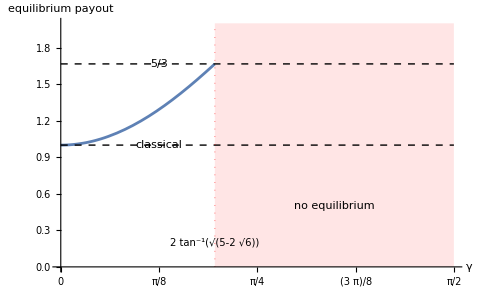

```mathematica
val=2 ArcTan[Sqrt[5-2 Sqrt[6]]];

Plot[Piecewise[{{2-Cos[2 γ],γ<=val}},-1],{γ,0,Pi/2},PlotRange->{0,2},AxesLabel->{"γ","equilibrium payout"},Ticks->{Range[0,Pi/2,Pi/8],Automatic},Prolog->{{Red,Opacity[0.1],Rectangle[{val,0},{Pi/2,2}]}},Epilog->{(*Horizontal Lines*){Dashed,Thin,Line[{{0,1},{Pi/2,1}}]},{Dashed,Thin,Line[{{0,5/3},{Pi/2,5/3}}]},(*Labels*)Text["classical",{Pi/8,1},{0,-1.5}],Text["5/3",{Pi/8,5/3},{0,-1.5}],Text["no equilibrium",{(val+Pi/2)/2,0.5}],(*Vertical Line and Formula Label*){Red,Dotted,Opacity[0.5],Line[{{val,0},{val,2}}]},Text[Style[HoldForm[2 ArcTan[Sqrt[5-2 Sqrt[6]]]],10],{val,0.2},{1.2,0}]}]
```